```mathematica
(*fl="/Users/ranza/Projects/Quantum/nitro-prome-128/nitrogen-3e-test/Results/RE_0_.datb0";*)
fl="/Users/ranza/Projects/Quantum/QSF-examples/nitrogen-3e/Results/RE_0_.datb0";

st=OpenRead[fl,BinaryFormat->True];
redata=BinaryReadList[st,"Real64"];
Close[fl];
Echo[Dimensions@redata,"dim"];
```

dim  {2528}

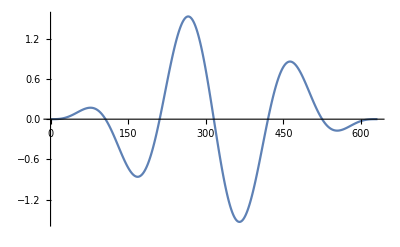

```mathematica
ListLinePlot[Partition[redata,4][[All,3]] ]
```

```mathematica
0.12 ω (*Sqrt[2/3.]*)
```

0.0072

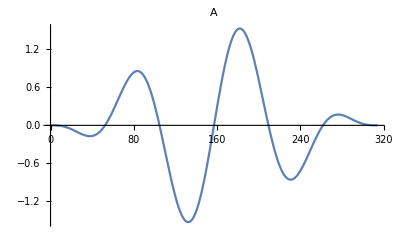

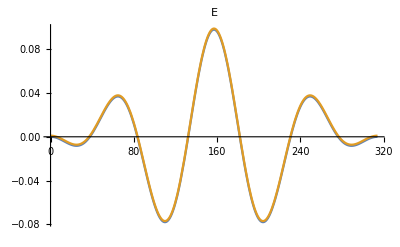

```mathematica
ω=0.06;
nc=3;
tp=nc 2π/ω;
F0=0.12 Sqrt[2/3.];
phi=0;
Plot[F0/ω  Sin[(π t)/tp]^2 Sin[phi+ω t-π*nc],{t,0,tp},PlotLabel->"A"]
Plot[{F0 Sin[(π t)/tp] (Cos[phi-nc π+t ω] Sin[(π t)/tp]+(2 π Cos[(π t)/tp] Sin[phi-nc π+t ω])/(tp ω)),Sin[(ω t)/(2nc)] F0(Sin[(ω t)/(2nc)]Cos[phi-nc π+ω t]+Cos[(ω t)/(2nc)]Sin[phi-nc π+t ω]/nc)+0.001},{t,0,tp},PlotLabel->"E"]
```

```mathematica
ω=.;
nc=.;
phi=.;
tp=.;(*nc 2π/ω;*)
F0=.;
FullSimplify[D[F0/ω Sin[(π t)/tp]^2 Sin[ω t-π*nc+phi],t]]
```

F0 Sin[(π t)/tp] (Cos[phi-nc π+t ω] Sin[(π t)/tp]+(2 π Cos[(π t)/tp] Sin[phi-nc π+t ω])/(tp ω))

```mathematica
Solve[{NE * EE==-a,EE*EE==b},{NE,EE},Reals]
```

{{NE→ConditionalExpression[-a/(√b), b>0],EE→ConditionalExpression[√b, b>0]},{NE→ConditionalExpression[a/(√b), b>0],EE→ConditionalExpression[-√b, b>0]}}